## Fun and Games

## Input Files (run twice)

```mathematica
ClearAll[ErrorListPlot]
```

```mathematica
<<"ErrorBarPlots`"
```

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

```mathematica
<<"ComputerArithmetic`"
```

```mathematica
ClearAll[ErrorListPlot]
```

```mathematica
<<"ErrorBarPlots`"
```

```mathematica
<<"ComputerArithmetic`"
```

## Lambda

### input

#### Inputing correlators

```mathematica
SetDirectory["/home/stephan/Nextcloud/2.Quarter/PHYS600/data"];
```

```mathematica
Import["cl3_32_48_b6p1_um0p2450_sm0p2450_RUN1_iso_data-reim.h5"];
```

```mathematica
Ls=Import["cl3_32_48_b6p1_um0p2450_sm0p2450_RUN1_iso_data-reim.h5",{"Datasets","/lam/Nx"}][[1]]
Import["cl3_32_48_b6p1_um0p2450_sm0p2450_RUN1_iso_data-reim.h5",{"Datasets","/lam/pz"}]
Import["cl3_32_48_b6p1_um0p2450_sm0p2450_RUN1_iso_data-reim.h5",{"Datasets","/lam/q"}]
```

32

{0}

{1,0,0,1,1,-1,0}

```mathematica
blahh5=Import["cl3_32_48_b6p1_um0p2450_sm0p2450_RUN1_iso_data-reim.h5",{"Datasets","/pp/C_re"}];
```

```mathematica
blahh5[[1]]
```

{{{0.0000341461,0.000187362,0.000342747,0.000209032,8.73583×10^-8,4.54736×10^-7,7.89432×10^-7,4.57057×10^-7}},{{3.61327×10^-6,0.0000193904,0.0000346956,0.000020699,4.48157×10^-9,2.25838×10^-8,3.79661×10^-8,2.12921×10^-8}},{{2.91018×10^-7,1.52117×10^-6,2.65153×10^-6,1.54113×10^-6,2.91611×10^-10,1.42012×10^-9,2.30779×10^-9,1.2514×10^-9}},{{2.29396×10^-8,1.16442×10^-7,1.97131×10^-7,1.1129×10^-7,2.37647×10^-11,1.1225×10^-10,1.76984×10^-10,9.31454×10^-11}},{{1.88823×10^-9,9.31322×10^-9,1.53227×10^-8,8.40752×10^-9,1.88947×10^-12,8.6662×10^-12,1.32756×10^-11,6.79227×10^-12}},{{1.51195×10^-10,7.22764×10^-10,1.15236×10^-9,6.12602×10^-10,1.45804×10^-13,6.45828×10^-13,9.56166×10^-13,4.73177×10^-13}},{{1.22597×10^-11,5.67201×10^-11,8.75137×10^-11,4.50071×10^-11,1.30642×10^-14,5.66389×10^-14,8.21224×10^-14,3.98159×10^-14}},{{1.02412×10^-12,4.58005×10^-12,6.82199×10^-12,3.37999×10^-12,1.12674×10^-15,4.71462×10^-15,6.585×10^-15,3.06748×10^-15}},{{9.12021×10^-14,3.94467×10^-13,5.66758×10^-13,2.69952×10^-13,9.91604×10^-17,4.00259×10^-16,5.36077×10^-16,2.37686×10^-16}},{{7.80961×10^-15,3.26581×10^-14,4.52982×10^-14,2.0799×10^-14,7.349×10^-18,2.83864×10^-17,3.64415×10^-17,1.55563×10^-17}},{{7.29096×10^-16,2.97176×10^-15,4.01956×10^-15,1.80339×10^-15,8.48045×10^-19,3.29704×10^-18,4.30202×10^-18,1.88824×10^-18}},{{6.81833×10^-17,2.67718×10^-16,3.48016×10^-16,1.49677×10^-16,8.2189×10^-20,2.99048×10^-19,3.67089×10^-19,1.52234×10^-19}},{{6.48786×10^-18,2.44305×10^-17,3.03793×10^-17,1.24869×10^-17,7.77735×10^-21,2.72818×10^-20,3.24766×10^-20,1.33684×10^-20}},{{6.47581×10^-19,2.35934×10^-18,2.85099×10^-18,1.15614×10^-18,6.09555×10^-22,2.10879×10^-21,2.55188×10^-21,1.10919×10^-21}},{{5.72428×10^-20,2.10575×10^-19,2.62347×10^-19,1.1161×10^-19,6.76605×10^-23,2.35359×10^-22,2.93075×10^-22,1.23592×10^-22}},{{2.9366×10^-21,1.20458×10^-20,1.85829×10^-20,1.02168×10^-20,-3.18155×10^-25,7.05556×10^-25,7.3872×10^-24,7.32754×10^-24}},{{1.4737×10^-22,6.10847×10^-22,1.14865×10^-21,7.48348×10^-22,-1.48577×10^-25,-3.06457×10^-26,8.72159×10^-25,6.25253×10^-25}},{{-1.46744×10^-23,-2.64484×10^-23,4.59426×10^-23,6.305×10^-23,-4.07673×10^-26,-9.87268×10^-26,6.64177×10^-26,1.18517×10^-25}},{{6.18367×10^-26,2.63973×10^-24,1.39939×10^-23,1.17877×10^-23,6.07856×10^-27,1.47056×10^-26,2.11378×10^-26,1.28193×10^-26}},{{2.80214×10^-25,7.48908×10^-25,1.40209×10^-24,9.97463×10^-25,1.09086×10^-27,2.65635×10^-27,1.93407×10^-27,4.47425×10^-28}},{{6.50923×10^-26,1.74455×10^-25,1.67889×10^-25,6.86268×10^-26,1.46944×10^-28,4.08304×10^-28,2.85304×10^-28,-1.26073×10^-29}},{{1.09891×10^-26,3.28179×10^-26,2.80889×10^-26,1.97498×10^-27,3.2754×10^-29,1.52615×10^-28,2.24387×10^-28,7.91322×10^-29}},{{1.84189×10^-27,6.53814×10^-27,7.12883×10^-27,1.37667×10^-27,2.68404×10^-30,1.35074×10^-29,1.59922×10^-29,1.59781×10^-30}},{{2.21278×10^-28,7.99189×10^-28,1.12868×10^-27,3.57255×10^-28,7.3738×10^-31,1.58767×10^-30,6.29749×10^-31,-4.42784×10^-31}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.}}}

```mathematica
Nconfigs=Length[blahh5]
Ntime=Length[blahh5[[1]]]
JNsigrat=N[Sqrt[(Nconfigs-1)^2/Nconfigs]];
```

3050

48

```mathematica
pionfile1=blahh5;
```

#### separate out the sources

```mathematica
ClearAll[pion1A,pion1sf];

pion1A={};
Do[
ClearAll[testa];
testa=Table[{kk-1,( Flatten[pionfile1[[ll]][[kk]]][[1]])},{kk,1,  Ntime}];
pion1A=Append[pion1A,testa];
,{ll,1,Nconfigs}];
pion1S1=pion1A;
```

```mathematica
ClearAll[pion1A,pion1sf];

pion1A={};
Do[
ClearAll[testa];
testa=Table[{kk-1,( Flatten[pionfile1[[ll]][[kk]]][[2]])},{kk,1,  Ntime}];
pion1A=Append[pion1A,testa];
,{ll,1,Nconfigs}];
pion1S2=pion1A;
```

#### Block in units of 20

```mathematica
ClearAll[merdeA,n,barf];
n=0;
merdeA={};
While[n<2118,
ClearAll[barf];
barf=Table[{pion1S1[[1]][[timen]][[1]],Sum[pion1S1[[kk]][[timen]][[2]],{kk,1+n,20+n}]},{timen,1,Ntime}];
merdeA=Append[merdeA,barf];
n=n+20];
pion1S1=merdeA;
```

```mathematica
ClearAll[merdeA,n,barf];
n=0;
merdeA={};
While[n<2118,
ClearAll[barf];
barf=Table[{pion1S2[[1]][[timen]][[1]],Sum[pion1S2[[kk]][[timen]][[2]],{kk,1+n,20+n}]},{timen,1,Ntime}];
merdeA=Append[merdeA,barf];
n=n+20];
pion1S2=merdeA;
```

```mathematica
Length[pion1S1]
```

106

```mathematica
pion1S1
```

{{{0,0.000654333},{1,0.0000709634},{2,6.02194×10^-6},{3,4.99774×10^-7},{4,4.22825×10^-8},{5,3.65248×10^-9},{6,3.22071×10^-10},{7,2.84206×10^-11},{8,2.53858×10^-12},{9,2.3161×10^-13},{10,2.10873×10^-14},{11,1.86587×10^-15},{12,1.64853×10^-16},{13,1.42989×10^-17},{14,1.28814×10^-18},{15,1.18366×10^-19},16,{32,0.},{33,0.},{34,0.},{35,0.},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.},{46,0.},{47,0.}},104,{1}}
 |  |  |  |

```mathematica
Nconfigs=Length[pion1S1];
JNsigrat=N[Sqrt[(Nconfigs-1)^2/Nconfigs]];
```

```mathematica
pion1S1[[1]]//TableForm
```

0 | 0.000654333
1 | 0.0000709634
2 | 6.02194×10^-6
3 | 4.99774×10^-7
4 | 4.22825×10^-8
5 | 3.65248×10^-9
6 | 3.22071×10^-10
7 | 2.84206×10^-11
8 | 2.53858×10^-12
9 | 2.3161×10^-13
10 | 2.10873×10^-14
11 | 1.86587×10^-15
12 | 1.64853×10^-16
13 | 1.42989×10^-17
14 | 1.28814×10^-18
15 | 1.18366×10^-19
16 | 1.29036×10^-20
17 | 1.35128×10^-21
18 | 1.17683×10^-22
19 | 1.16358×10^-23
20 | 1.58137×10^-24
21 | 2.94895×10^-25
22 | 3.68152×10^-26
23 | 2.8659×10^-27
24 | 0.
25 | 0.
26 | 0.
27 | 0.
28 | 0.
29 | 0.
30 | 0.
31 | 0.
32 | 0.
33 | 0.
34 | 0.
35 | 0.
36 | 0.
37 | 0.
38 | 0.
39 | 0.
40 | 0.
41 | 0.
42 | 0.
43 | 0.
44 | 0.
45 | 0.
46 | 0.
47 | 0.

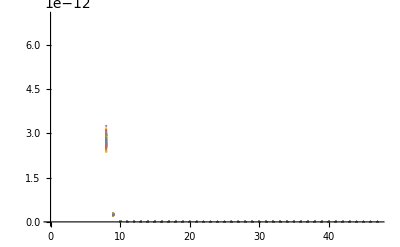

```mathematica
ListPlot[pion1S1]
```

```mathematica
Export["../data/nndata.h5",pion1S1]
```

../data/nndata.h5